{{p[t]→InterpolatingFunction[{{0., 12.}}, <>][t],y[t]→InterpolatingFunction[{{0., 12.}}, <>][t],z[t]→InterpolatingFunction[{{0., 12.}}, <>][t],a[t]→InterpolatingFunction[{{0., 12.}}, <>][t]}}

{{0.872722}}

{{17.2939}}

{{0.913972}}

{{1.03764}}

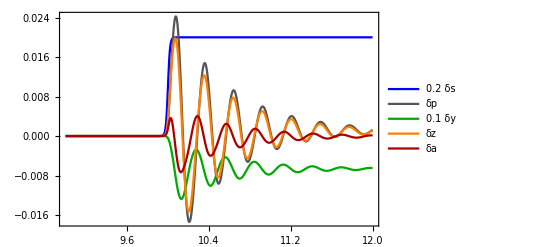

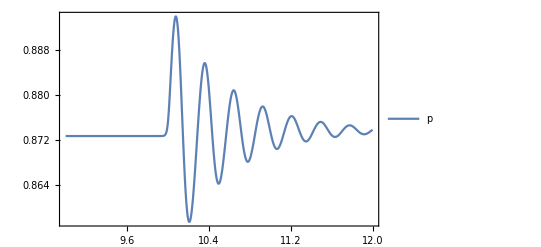

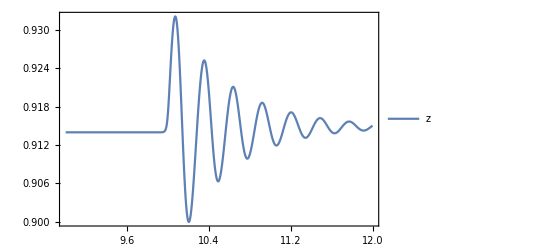

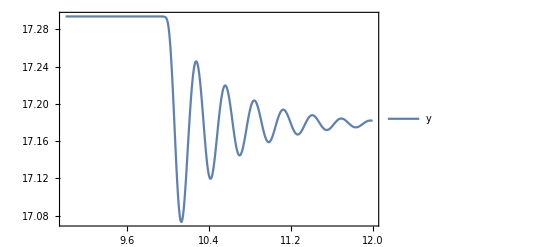

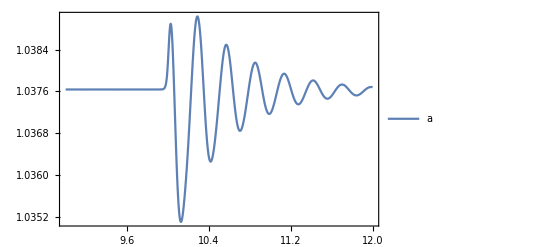

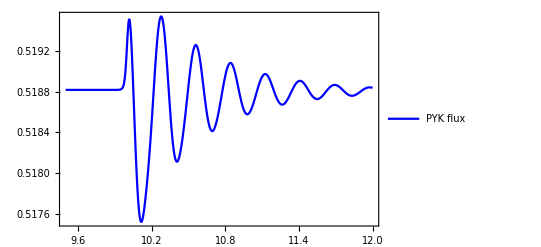

```mathematica
(*This is my system used in paper, signal as perturbation*)
ClearAll["Global`*"]
hill=1000;t0=10;maxTime=12;
h=3;τ=0.01;α1=1;α2=1;ϵ=0.01;
ds=0.01;
s0=0.04;
w=17;
s[t_]:=s0(1+ds*t^hill/(t0^hill+t^hill));
(*s[t_]:=s0+ds*Sin[w t];*)
(*(0.5+s[t]^2/(1+s[t]^2))*)
basal=0.02;
timeCourse=NDSolve[{τ p'[t]==-2  p[t]/(1+p[t]^(2 h))+4  z[t]/(1+p[t]^2 )-2p[t]^2/(1+p[t]^2), τ y'[t]==2 p[t]/(1+p[t]^(2 h))- y[t]*(α1 s[t]+basal)-ϵ y[t],τ z'[t]== y[t]*(α1 s[t]+basal)-2  z[t]/(1+p[t]^2 ),τ a'[t]==2 z[t]/(1+p[t]^2 )-α2 a[t],p[0]==1,y[0]==1/(s0+basal),z[0]==1,a[0]==1},{p[t],y[t],z[t],a[t]},{t,0,maxTime}]
pSol[t_]:=p[t]/.timeCourse;
ySol[t_]:=y[t]/.timeCourse;
zSol[t_]:=z[t]/.timeCourse;
aSol[t_]:=a[t]/.timeCourse;
PYKflux[t_]:=z[t]/(1+p[t]^2)/.timeCourse
a0=Table[pSol[t],{t,{t0-3}}] (*ATP concentration*)
y0=Table[ySol[t],{t,{t0-3}}](*intermediate metabolite: TRIO*)
z0=Table[zSol[t],{t,{t0-3}}](*intermediate metabolite: TRIO*)
f0=Table[aSol[t],{t,{t0-3}}](*intermediate metabolite: TRIO*)
Plot[{2(s[t]-s0)/s0,(pSol[t]-a0)/a0,(ySol[t]-y0)/y0,(zSol[t]-z0)/z0,3(aSol[t]-f0)/f0},{t,9,maxTime},PlotStyle->{Blue,Lighter[Black],Darker[Green],Orange,Darker[Red]},PlotRange->All,PlotLegends->{"0.2 δs","δp","0.1 δy","δz","δa"},BaseStyle->{FontSize->18},Frame->True]

Plot[{pSol[t]},{t,9,maxTime},PlotLegends->{"p"},PlotRange->All,BaseStyle->{FontSize->18},Frame->True]
Plot[{zSol[t]},{t,9,maxTime},PlotLegends->{"z"},PlotRange->All,BaseStyle->{FontSize->18},Frame->True]
Plot[{ySol[t]},{t,9,maxTime},PlotLegends->{"y"},BaseStyle->{FontSize->18},PlotRange->All,Frame->True]
Plot[{aSol[t]},{t,9,maxTime},PlotLegends->{"a"},BaseStyle->{FontSize->18},PlotRange->All,Frame->True]

Plot[{PYKflux[t]},{t,9.5,maxTime},PlotLegends->{"PYK flux"},PlotStyle->{Blue},BaseStyle->{FontSize->18},PlotRange->All,Frame->True]
```

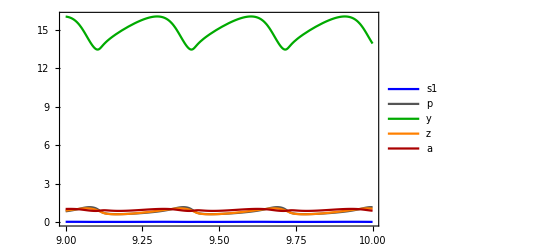

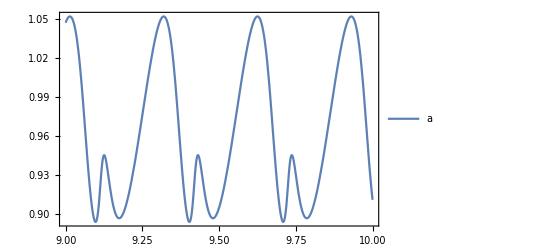

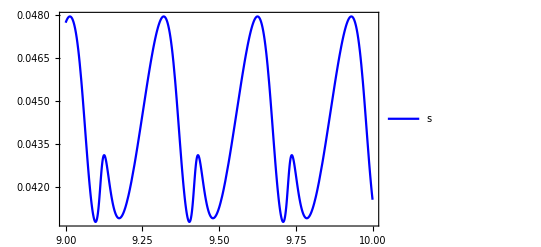

{{0.910853}}

```mathematica
(*This is my new system used in paper, including signal dynamics, assuming fast signal diffusion across the cell membrane*)
ClearAll["Global`*"]
maxTime=10; t0=9;
h=3;τ=0.01;α1=1;α2=1; ϵ=0.01;
 s0=2; k1=0.5;k2=0.3;ϕ=0.014;d=0.001;
(*h=3;τ=1;α1=1;α2=1; ϵ=0.01;
 k1=0.5;k2=0.1;ϕ=0.05;d=0.1;*)

basal=0.02;
timeCourse=NDSolve[{τ p'[t]==-2  p[t]/(1+p[t]^(2 h))+4  z[t]/(1+p[t]^2 )-2 p[t]^2/(1+p[t]^2),τ y'[t]==2 p[t]/(1+p[t]^(2 h))-α1 y[t](basal+s1[t])-ϵ y[t],τ z'[t]==α1 y[t](basal+ s1[t])-2  z[t]/(1+p[t]^2 ),τ a'[t]==2 z[t]/(1+p[t]^2 )-α2 a[t],d τ s1'[t]== ϕ/(1+ϕ) α2 a[t]-(ϕ k1+k2)/(ϕ+1) s1[t],p[0]==1.01,y[0]==1/s0,z[0]==1,a[0]==1,s1[0]==s0},{p[t],y[t],z[t],a[t],s1[t]},{t,0,maxTime}];
s1Sol[t_]:=s1[t]/.timeCourse;
pSol[t_]:=p[t]/.timeCourse;
ySol[t_]:=y[t]/.timeCourse;
zSol[t_]:=z[t]/.timeCourse;
aSol[t_]:=a[t]/.timeCourse;
(*a0=Mean[Table[pSol[t],{t,Array[0.01#1+t0-3&,100]}] ];(*ATP concentration*)
y0=Mean[Table[ySol[t],{t,Array[0.01#1+t0-3&,100]}]];(*intermediate metabolite: TRIO*)
z0=Mean[Table[zSol[t],{t,Array[0.01#1+t0-3&,100]}]];(*intermediate metabolite: TRIO*)
f0=Mean[Table[aSol[t],{t,Array[0.01#1+t0-3&,100]}]];(*intermediate metabolite: TRIO*)
s0=Mean[Table[sSol[t],{t,Array[0.01#1+t0-3&,500]}]];
varS0=StandardDeviation[Table[sSol[t],{t,Array[0.01#1+t0-3&,100]}]];
varS0=StandardDeviation[Table[sSol[t],{t,Array[0.01#1+t0-3&,100]}]]
Plot[{(sSol[t]-s0)/s0,(pSol[t]-a0)/a0,(ySol[t]-y0)/y0,(zSol[t]-z0)/z0,(aSol[t]-f0)/f0},{t,9,maxTime},PlotRange->All,PlotLegends->{"s","p","y","z","a"},BaseStyle->{FontSize->18},Frame->True]*)
Plot[{s1Sol[t],pSol[t],ySol[t],zSol[t],aSol[t]},{t,t0,maxTime},PlotRange->Full,PlotLegends->{"s1","p","y","z","a"},PlotStyle->{Blue,Lighter[Black],Darker[Green],Orange,Darker[Red]},BaseStyle->{FontSize->18},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]
Plot[{aSol[t]},{t,t0,maxTime},PlotRange->Full,PlotLegends->{"a"},BaseStyle->{FontSize->18},Frame->True]
Plot[{s1Sol[t]},{t,t0,maxTime},PlotRange->Full,PlotLegends->{"s"},BaseStyle->{FontSize->18},PlotStyle->{Blue},Frame->True]
N[Table[aSol[t],{t,{10}}]]
```

```mathematica
(*******Collective oscillations against yeast cell density, assuming fast signal diffusion across the membrane*******)
ClearAll["Global`*"]
maxTime=20; t0=10;
h=3;τ=0.01;α1=1;α2=1; ϵ=0.01;
 k1=0.5;k2=0.3;d=0.001;
basal=0.02;
maxN=100;
phi=Array[0.01 #1-0.01 &,maxN];varS0=Array[0 #1 &,maxN];varf0=Array[0 #1 &,maxN];s0Array=Array[0 #1 &,maxN];f0Array=Array[0 #1 &,maxN];
For[j=1,j<maxN+1,j++,ϕ=phi[[j]];
timeCourse=NDSolve[{τ p'[t]==-2  p[t]/(1+p[t]^(2 h))+4  z[t]/(1+p[t]^2 )-2 p[t]^2/(1+p[t]^2),τ y'[t]==2 p[t]/(1+p[t]^(2 h))-α1 y[t](basal+s1[t])-ϵ y[t],τ z'[t]==α1 y[t] (basal+s1[t])-2  z[t]/(1+p[t]^2 ),τ a'[t]==2 z[t]/(1+p[t]^2 )-α2 a[t],d τ s1'[t]== ϕ/(1+ϕ) α2 a[t]-(ϕ k1+k2)/(ϕ+1) s1[t],p[0]==1.01,y[0]==1,z[0]==1,a[0]==1,s1[0]==1},{p[t],y[t],z[t],a[t],s1[t]},{t,0,maxTime}];
sSol[t_]:=s1[t]/.timeCourse;
s0=Mean[Table[sSol[t],{t,Array[d#1+t0-3&,1000]}]];
s0Array[[j]]=s0;
varS0[[j]]=Max[Table[sSol[t]-s0,{t,Array[d#1+t0-3&,1000]}]];
aSol[t_]:=a[t]/.timeCourse;
f0=Mean[Table[aSol[t],{t,Array[d#1+t0-3&,1000]}]];
f0Array[[j]]=f0;
varf0[[j]]=Max[Table[aSol[t]-f0,{t,Array[d#1+t0-3&,1000]}]];
]
```

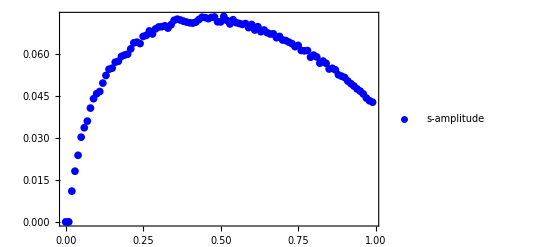

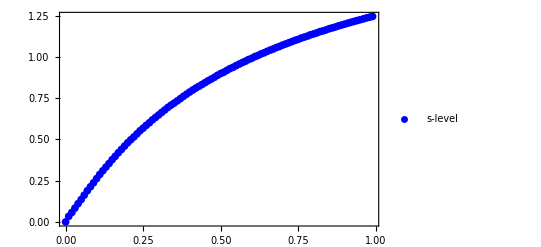

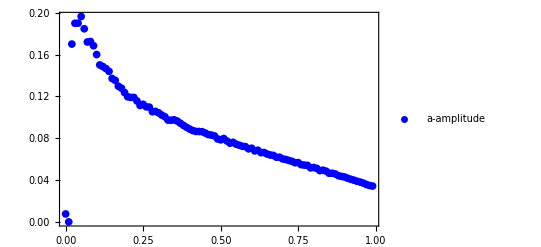

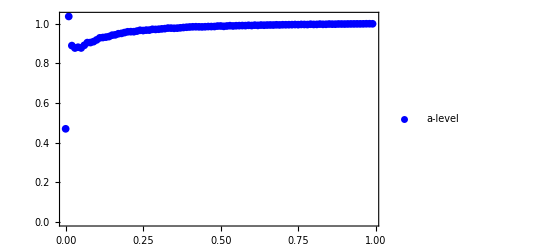

```mathematica
ListPlot[Thread[{phi,Flatten[varS0]}],PlotRange->All,PlotStyle->{Blue},PlotLegends->{"s-amplitude"},BaseStyle->{FontSize->18},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]
ListPlot[Thread[{phi,Flatten[s0Array]}],PlotRange->All,PlotStyle->{Blue},PlotLegends->{"s-level"},BaseStyle->{FontSize->18},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]
ListPlot[Thread[{phi,Flatten[varf0]}],PlotRange->All,PlotStyle->{Blue},PlotLegends->{"a-amplitude"},BaseStyle->{FontSize->18},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]
ListPlot[Thread[{phi,Flatten[f0Array]}],PlotRange->All,PlotStyle->{Blue},PlotLegends->{"a-level"},BaseStyle->{FontSize->18},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]
```

```mathematica
(*** collective dynamics, distinguish inner and outer signal concentration, change D1 ****)
ClearAll["Global`*"]
maxTime=20; t0=10;
h=3;τ=0.01;α1=1;α2=1; ϵ=0.01;
 k1=0.5;k2=0.3;d=0.001; D1=100;
basal=0.02;
maxN=100;
phi=Array[0.01 #1-0.01 &,maxN];
varS10=Array[0 #1 &,maxN];
varS20=Array[0 #1 &,maxN];varf0=Array[0 #1 &,maxN];s10Array=Array[0 #1 &,maxN];
s20Array=Array[0 #1 &,maxN];
f0Array=Array[0 #1 &,maxN];
For[j=1,j<maxN+1,j++,ϕ=phi[[j]];
timeCourse=NDSolve[{τ p'[t]==-2  p[t]/(1+p[t]^(2 h))+4  z[t]/(1+p[t]^2 )-2 p[t]^2/(1+p[t]^2),τ y'[t]==2 p[t]/(1+p[t]^(2 h))-α1 y[t](basal+s1[t])-ϵ y[t],τ z'[t]==α1 y[t] (basal+s1[t])-2  z[t]/(1+p[t]^2 ),τ a'[t]==2 z[t]/(1+p[t]^2 )-α2 a[t],d τ s1'[t]== α2 a[t]-k1 s1[t]-D1(s1[t]-s2[t]),d τ s2'[t]==ϕ D1(s1[t]-s2[t])-k2 s2[t],p[0]==1.01,y[0]==1,z[0]==1,a[0]==1,s1[0]==1,s2[0]==1},{p[t],y[t],z[t],a[t],s1[t],s2[t]},{t,0,maxTime}];
sSol1[t_]:=s1[t]/.timeCourse;
sSol2[t_]:=s2[t]/.timeCourse;
s10=Mean[Table[sSol1[t],{t,Array[d#1+t0-3&,1000]}]];
s20=Mean[Table[sSol2[t],{t,Array[d#1+t0-3&,1000]}]];
s10Array[[j]]=s10;
varS10[[j]]=Max[Table[sSol1[t]-s10,{t,Array[d#1+t0-3&,1000]}]];
s20Array[[j]]=s20;
varS20[[j]]=Max[Table[sSol2[t]-s20,{t,Array[d#1+t0-3&,1000]}]];
aSol[t_]:=a[t]/.timeCourse;
f0=Mean[Table[aSol[t],{t,Array[d#1+t0-3&,1000]}]];
f0Array[[j]]=f0;
varf0[[j]]=Max[Table[aSol[t]-f0,{t,Array[d#1+t0-3&,1000]}]];
]
```

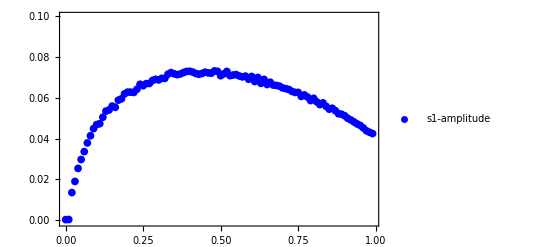

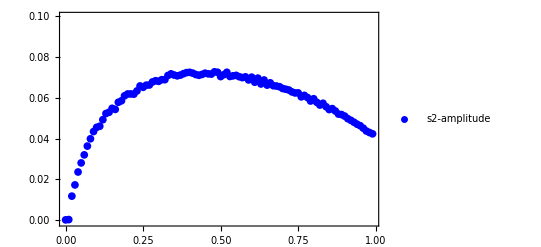

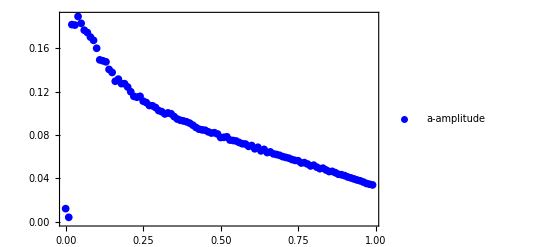

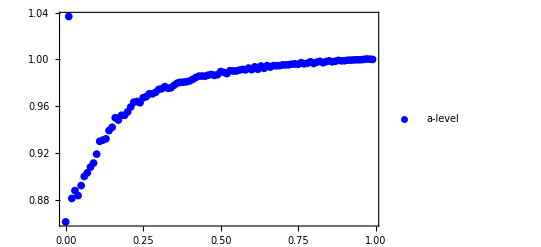

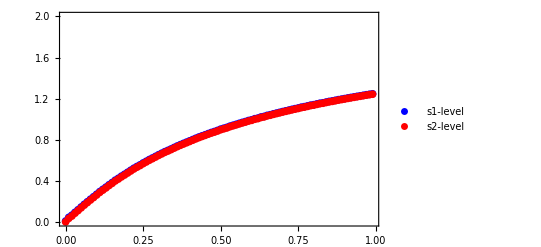

```mathematica
ListPlot[Thread[{phi,Flatten[varS10]}],PlotRange->{{-0.001,0.1}},PlotStyle->{Blue},PlotLegends->{"s1-amplitude"},BaseStyle->{FontSize->25},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]
ListPlot[Thread[{phi,Flatten[varS20]}],PlotRange->{{-0.001,0.1}},PlotStyle->{Blue},PlotLegends->{"s2-amplitude"},BaseStyle->{FontSize->25},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]
ListPlot[Thread[{phi,Flatten[varf0]}],PlotRange->All,PlotStyle->{Blue},PlotLegends->{"a-amplitude"},BaseStyle->{FontSize->18},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]
ListPlot[Thread[{phi,Flatten[f0Array]}],PlotRange->All,PlotStyle->{Blue},PlotLegends->{"a-level"},BaseStyle->{FontSize->18},Frame->True,LabelStyle->{FontFamily->"Helvetica"},PlotStyle->PointSize[0.03]]
ListPlot[{Thread[{phi,Flatten[s10Array]}],Thread[{phi,Flatten[s20Array]}]},PlotRange->{{0,2}},PlotStyle->{Blue,Red},PlotLegends->{"s1-level","s2-level"},BaseStyle->{FontSize->25},Frame->True,LabelStyle->{FontFamily->"Helvetica"}]
```